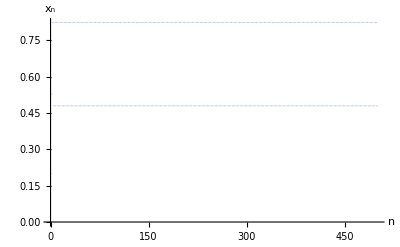

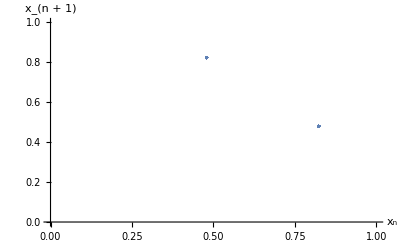

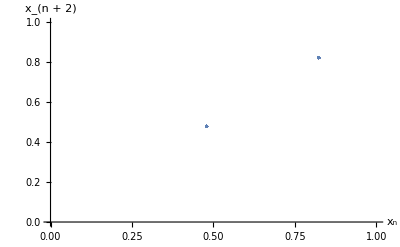

```mathematica
Clear["Global`*"]
r=3.3;
list=RecurrenceTable[{x[n+1]==r*x[n]*(1-x[n]),x[1]==.2},x,{n,1,500}];
ListPlot[list,AxesLabel->{"n","x_n"},PlotStyle-> PointSize[.001],AxesLabel->{"n","x_n"}]
lista=Part[list,200;;499];
listb=Part[list,201;;500];
changelist=Transpose[{lista,listb}];
ListPlot[changelist,PlotStyle-> PointSize[.005],AxesLabel->{"x_n","x_(n + 1)"},PlotRange->{{0,1},{0,1}}]
lista=Part[list,200;;498];
listb=Part[list,202;;500];
changelist=Transpose[{lista,listb}];
ListPlot[changelist,PlotStyle-> PointSize[.005],AxesLabel->{"x_n","x_(n + 2)"},PlotRange->{{0,1},{0,1}}]
```

```mathematica
S
```

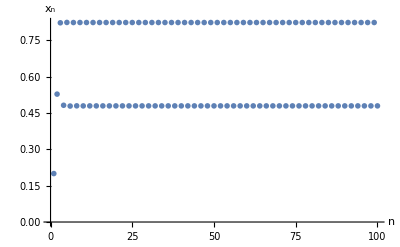

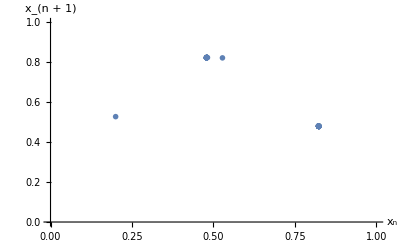

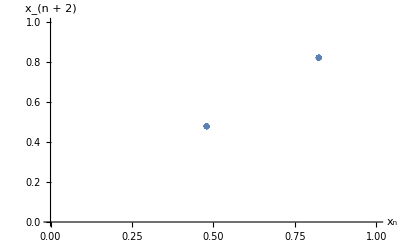

```mathematica
Clear["Global`*"]
r=3.3;
list=RecurrenceTable[{x[n+1]==r*x[n]*(1-x[n]),x[1]==.200001},x,{n,1,100}];
ListPlot[list,AxesLabel->{"n","x_n"},PlotStyle-> PointSize[.01]]
lista=Part[list,1;;99];
listb=Part[list,2;;100];
changelist=Transpose[{lista,listb}];
ListPlot[changelist,PlotStyle-> PointSize[.01],AxesLabel->{"x_n","x_(n + 1)"},PlotRange->{{0,1},{0,1}}]
lista=Part[list,30;;98];
listb=Part[list,32;;100];
changelist=Transpose[{lista,listb}];
ListPlot[changelist,PlotStyle-> PointSize[.01],AxesLabel->{"x_n","x_(n + 2)"},PlotRange->{{0,1},{0,1}}]
```